# Testing out DMFormFactor functions

```mathematica
SetDirectory["/home/farmer/mathematica/DMFormFactor_13086288"]
```

/home/farmer/mathematica/DMFormFactor_13086288

```mathematica
<<"v6/dmformfactor-V6.m";
```

Welcome to DMFormFactor version 1.1.

Functions are SetCoeffsNonrel, SetCoeffsRel, SetCoeffsNucl, ZeroCoeffs, SetJChi, SetMchi, SetIsotope, SetHALO, SetHelm, TransitionProbability, ResponseNucl, DiffCrossSection, ApproxTotalCrossSection, and EventRate.

## Event rate

Model setup

```mathematica
(* Model Setup *)
SetJChi[1/2](* WIMP spin *)
mchi=Mchi GeV
SetMChi[mchi](* WIMP mass in GeV *)
Xe131filename="default";  (* nuclear density matrix (using default density matrices) *)
bFM="default"; (* oscillation parameter (default: approximate formulae used) *)
A=131;
SetIsotope[54,A,bFM,Xe131filename] (*[Z,A,bFM,filename]*)
ZeroCoeffs[];(*Reset all coefficients*)
SetCoeffsNonrel[1,c1p,"p"]
SetCoeffsNonrel[1,c1n,"n"]
SetCoeffsNonrel[4,c4p,"p"]
SetCoeffsNonrel[4,c4n,"n"]
SetCoeffsNonrel[6,c6p,"p"]
SetCoeffsNonrel[6,c6n,"n"]
(* Set non-zero NR EFT coefficient values *)
```

GeV Mchi

Getting default matrix...

Setting isotope to xenon-131.

Attempting to compute a recoil spectrum...

```mathematica
(* Parameters *)
mNucleon=0.938 GeV;
mNucleus=A*mNucleon
NT=1/mNucleus;(*Number of target nuclei per detector mass*)
Centimeter=(10^13 Femtometer);
rhoDM=0.3GeV/Centimeter^3;(*Local dark matter density*)
ve=232 KilometerPerSecond;(*Earth's velocity in galactic rest frame*)
v0=220 KilometerPerSecond;(*Mean WIMP speed in galactic rest frame*)
SetHALO["MB"];(*using default MB Halo*)
```

122.878 GeV

```mathematica
1/246.2^2
```

0.0000164977

```mathematica
diffsigma=DiffCrossSection[ERkeV,v]
```

Your Lagrangian is

L_prot=0.+(0.0000187399 (S_χ·q)(S_N·q) c6p)/GeV^4+(0.0000164977 1 c1p)/GeV^2+(0.0000164977 S_χ·S_N c4p)/GeV^2

L_neut=0.+(0.0000187399 (S_χ·q)(S_N·q) c6n)/GeV^4+(0.0000164977 1 c1n)/GeV^2+(0.0000164977 S_χ·S_N c4n)/GeV^2

$Aborted

```mathematica
diffsigma=DiffCrossSection[ERkeV,v]
```

```mathematica
dRdE=EventRate[NT,rhoDM,qGeV,ve,v0]
```

Your Lagrangian is

L_prot=0.+(0.0000187399 (S_χ·q)(S_N·q) c6p)/GeV^4+(0.0000164977 1 c1p)/GeV^2+(0.0000164977 S_χ·S_N c4p)/GeV^2

L_neut=0.+(0.0000187399 (S_χ·q)(S_N·q) c6n)/GeV^4+(0.0000164977 1 c1n)/GeV^2+(0.0000164977 S_χ·S_N c4n)/GeV^2

Your event rate is

1/(GeV Mchi^3)2.6053×10^-44 (0.+646.112 ⅇ^(-67.4762 qGeV^2) (0.+1/16 (3.83376×10^-9 c4p^2 Mchi^2+8.70959×10^-9 c4p c6p Mchi^2 qGeV^2+4.94664×10^-9 c6p^2 Mchi^2 qGeV^4) (0.0000578995-0.00110472 qGeV^2+0.145001 qGeV^4-23.9866 qGeV^6+1134.14 qGeV^8-23107.7 qGeV^10+224088. qGeV^12-984096. qGeV^14+1.57479×10^6 qGeV^16-5.92859 qGeV^18+0.0000113549 qGeV^20)+2.3961×10^-10 c4p^2 Mchi^2 (0.000115799-0.0301499 qGeV^2+1.76061 qGeV^4+57.4599 qGeV^6-897.29 qGeV^8-51856.5 qGeV^10+1.18093×10^6 qGeV^12-7.92115×10^6 qGeV^14+1.70034×10^7 qGeV^16-191.821 qGeV^18+0.000569711 qGeV^20)+3.83376×10^-9 c1p^2 Mchi^2 (2915.98-354651. qGeV^2+1.66663×10^7 qGeV^4-3.89909×10^8 qGeV^6+4.97028×10^9 qGeV^8-3.52778×10^10 qGeV^10+1.35444×10^11 qGeV^12-2.55168×10^11 qGeV^14+1.83904×10^11 qGeV^16-134154. qGeV^18+0.0248999 qGeV^20)+1/16 (3.83376×10^-9 c4n c4p Mchi^2+8.70959×10^-9 c4p c6n Mchi^2 qGeV^2+4.94664×10^-9 c6n c6p Mchi^2 qGeV^4) (0.00225524+0.106455 qGeV^2-12.073 qGeV^4-29.6556 qGeV^6+24984.9 qGeV^8-773389. qGeV^10+9.78397×10^6 qGeV^12-5.59042×10^7 qGeV^14+1.14708×10^8 qGeV^16-2.13056×10^6 qGeV^18+6.86271 qGeV^20)+1/16 (3.83376×10^-9 c4n c4p Mchi^2+8.70959×10^-9 c4n c6p Mchi^2 qGeV^2+4.94664×10^-9 c6n c6p Mchi^2 qGeV^4) (0.00225524+0.106455 qGeV^2-12.073 qGeV^4-29.6556 qGeV^6+24984.9 qGeV^8-773389. qGeV^10+9.78397×10^6 qGeV^12-5.59042×10^7 qGeV^14+1.14708×10^8 qGeV^16-2.13056×10^6 qGeV^18+6.86271 qGeV^20)+4.7922×10^-10 c4n c4p Mchi^2 (0.00451048-1.30077 qGeV^2+107.856 qGeV^4-1443.82 qGeV^6-100302. qGeV^8+3.81807×10^6 qGeV^10-5.10723×10^7 qGeV^12+2.91685×10^8 qGeV^14-5.90895×10^8 qGeV^16-5.32206×10^7 qGeV^18+307.518 qGeV^20)+7.66753×10^-9 c1n c1p Mchi^2 (4157.7-551594. qGeV^2+2.86787×10^7 qGeV^4-7.57984×10^8 qGeV^6+1.12026×10^10 qGeV^8-9.54998×10^10 qGeV^10+4.63347×10^11 qGeV^12-1.19651×10^12 qGeV^14+1.39184×10^12 qGeV^16-4.64714×10^11 qGeV^18+170015. qGeV^20)+1/16 (3.83376×10^-9 c4n^2 Mchi^2+8.70959×10^-9 c4n c6n Mchi^2 qGeV^2+4.94664×10^-9 c6n^2 Mchi^2 qGeV^4) (0.0878436+9.96911 qGeV^2-264.17 qGeV^4-17861.1 qGeV^6+1.61079×10^6 qGeV^8-4.68721×10^7 qGeV^10+6.461×10^8 qGeV^12-4.27656×10^9 qGeV^14+1.11665×10^10 qGeV^16-4.34684×10^8 qGeV^18+4.29089×10^6 qGeV^20)+2.3961×10^-10 c4n^2 Mchi^2 (0.175687-55.5895 qGeV^2+6549.51 qGeV^4-372689. qGeV^6+1.1805×10^7 qGeV^8-2.12171×10^8 qGeV^10+2.11089×10^9 qGeV^12-1.06654×10^10 qGeV^14+2.0847×10^10 qGeV^16+3.72292×10^9 qGeV^18+1.68457×10^8 qGeV^20)+3.83376×10^-9 c1n^2 Mchi^2 (5928.2-851956. qGeV^2+4.86226×10^7 qGeV^4-1.43569×10^9 qGeV^6+2.42258×10^10 qGeV^8-2.42602×10^11 qGeV^10+1.43964×10^12 qGeV^12-4.84312×10^12 qGeV^14+8.236×10^12 qGeV^16-5.41182×10^12 qGeV^18+1.17492×10^12 qGeV^20)) (Erf[1.05455-(5.54336 (122.914 GeV+GeV Mchi) qGeV)/(GeV Mchi)]+Erf[1.05455+(5.54336 (122.914 GeV+GeV Mchi) qGeV)/(GeV Mchi)]))

```mathematica
diffsigma//Simplify[#,{Element[GeV,Reals],GeV>0}]&
```

1/(GeV^3 v^2)0.0868006 ⅇ^(-0.0165875 ERkeV) ((3.83376×10^-9 c4p^2+2.14106×10^-12 c4p c6p ERkeV+2.98931×10^-16 c6p^2 ERkeV^2) (0.0000578995-2.7157×10^-7 ERkeV+8.76254×10^-9 ERkeV^2-3.56335×10^-10 ERkeV^3+4.14178×10^-12 ERkeV^4-2.07447×10^-14 ERkeV^5+4.94538×10^-17 ERkeV^6-5.33885×10^-20 ERkeV^7+2.10022×10^-23 ERkeV^8-1.94367×10^-32 ERkeV^9+9.15133×10^-42 ERkeV^10)+3.83376×10^-9 c4p^2 (0.000115799-7.41167×10^-6 ERkeV+1.06396×10^-7 ERkeV^2+8.53601×10^-10 ERkeV^3-3.27682×10^-12 ERkeV^4-4.65536×10^-14 ERkeV^5+2.60619×10^-16 ERkeV^6-4.29733×10^-19 ERkeV^7+2.26765×10^-22 ERkeV^8-6.28877×10^-31 ERkeV^9+4.5915×10^-40 ERkeV^10)+6.13402×10^-8 c1p^2 (2915.98-87.183 ERkeV+1.00716 ERkeV^2-0.00579233 ERkeV^3+0.000018151 ERkeV^4-3.16702×10^-8 ERkeV^5+2.98911×10^-11 ERkeV^6-1.38432×10^-14 ERkeV^7+2.45262×10^-18 ERkeV^8-4.39818×10^-28 ERkeV^9+2.00677×10^-38 ERkeV^10)+(3.83376×10^-9 c4n c4p+2.14106×10^-12 c4n c6p ERkeV+2.98931×10^-16 c6n c6p ERkeV^2) (0.00225524+0.0000261696 ERkeV-7.29581×10^-7 ERkeV^2-4.40552×10^-10 ERkeV^3+9.12428×10^-11 ERkeV^4-6.94302×10^-13 ERkeV^5+2.15921×10^-15 ERkeV^6-3.03288×10^-18 ERkeV^7+1.5298×10^-21 ERkeV^8-6.98496×10^-27 ERkeV^9+5.5309×10^-36 ERkeV^10)+7.66753×10^-9 c4n c4p (0.00451048-0.000319764 ERkeV+6.51785×10^-6 ERkeV^2-2.14488×10^-8 ERkeV^3-3.66292×10^-10 ERkeV^4+3.42763×10^-12 ERkeV^5-1.12711×10^-14 ERkeV^6+1.58243×10^-17 ERkeV^7-7.88045×10^-21 ERkeV^8-1.74482×10^-25 ERkeV^9+2.47839×10^-34 ERkeV^10)+1.2268×10^-7 c1n c1p (4157.7-135.597 ERkeV+1.73308 ERkeV^2-0.0112603 ERkeV^3+0.000040911 ERkeV^4-8.57339×10^-8 ERkeV^5+1.02256×10^-10 ERkeV^6-6.49124×10^-14 ERkeV^7+1.85622×10^-17 ERkeV^8-1.52355×10^-21 ERkeV^9+1.37021×10^-31 ERkeV^10)+(3.83376×10^-9 c4n^2+2.14106×10^-12 c4n c6n ERkeV+2.98931×10^-16 c6n^2 ERkeV^2) (0.0878436+0.00245068 ERkeV-0.0000159641 ERkeV^2-2.65337×10^-7 ERkeV^3+5.88245×10^-9 ERkeV^4-4.20789×10^-11 ERkeV^5+1.42587×10^-13 ERkeV^6-2.32009×10^-16 ERkeV^7+1.48921×10^-19 ERkeV^8-1.4251×10^-24 ERkeV^9+3.45818×10^-30 ERkeV^10)+3.83376×10^-9 c4n^2 (0.175687-0.0136654 ERkeV+0.000395794 ERkeV^2-5.53652×10^-6 ERkeV^3+4.3111×10^-8 ERkeV^4-1.90474×10^-10 ERkeV^5+4.6585×10^-13 ERkeV^6-5.78615×10^-16 ERkeV^7+2.78025×10^-19 ERkeV^8+1.22055×10^-23 ERkeV^9+1.35766×10^-28 ERkeV^10)+6.13402×10^-8 c1n^2 (5928.2-209.434 ERkeV+2.93831 ERkeV^2-0.0213281 ERkeV^3+0.0000884704 ERkeV^4-2.17794×10^-7 ERkeV^5+3.17712×10^-10 ERkeV^6-2.62746×10^-13 ERkeV^7+1.09839×10^-16 ERkeV^8-1.77424×10^-20 ERkeV^9+9.46908×10^-25 ERkeV^10)+(0.00225524+0.0000261696 ERkeV-7.29581×10^-7 ERkeV^2-4.40552×10^-10 ERkeV^3+9.12428×10^-11 ERkeV^4-6.94302×10^-13 ERkeV^5+2.15921×10^-15 ERkeV^6-3.03288×10^-18 ERkeV^7+1.5298×10^-21 ERkeV^8-6.98496×10^-27 ERkeV^9+5.5309×10^-36 ERkeV^10) (3.83376×10^-9 c4n c4p+c6n ERkeV (2.14106×10^-12 c4p+2.98931×10^-16 c6p ERkeV)))

```mathematica
(*Isn't it weird that the differential cross section doesn't depend on the WIMP mass?*)
```

```mathematica
simpdsig = diffsigma/.{c1n->c1p}/.{c4n->c4p}/.{c6n->c6p}/.v->220KilometerPerSecond/.c1p->0/.c4p->0/.c6p->10^-8//Simplify[#,{Element[GeV,Reals],GeV>0}]&
```

1/GeV^3 ⅇ^(-0.0165875 ERkeV) ERkeV^2 (4.45275×10^-28+1.20591×10^-29 ERkeV-8.39094×10^-32 ERkeV^2-1.28445×10^-33 ERkeV^3+2.92431×10^-35 ERkeV^4-2.09542×10^-37 ERkeV^5+7.08083×10^-40 ERkeV^6-1.14739×10^-42 ERkeV^7+7.32401×10^-46 ERkeV^8-6.93395×10^-51 ERkeV^9+1.66628×10^-56 ERkeV^10)

```mathematica
dRdEsimp=Simplify[dRdE,{Element[GeV,Reals],GeV>0,Element[Mchi,Reals],Mchi>0,Element[qGeV,Reals],qGeV>0}]
```

1/(GeV Mchi)1.05207×10^-42 ⅇ^(-67.4762 qGeV^2) ((3.83376×10^-9 c4p^2+8.70959×10^-9 c4p c6p qGeV^2+4.94664×10^-9 c6p^2 qGeV^4) (0.0000578995-0.00110472 qGeV^2+0.145001 qGeV^4-23.9866 qGeV^6+1134.14 qGeV^8-23107.7 qGeV^10+224088. qGeV^12-984096. qGeV^14+1.57479×10^6 qGeV^16-5.92859 qGeV^18+0.0000113549 qGeV^20)+1.52736×10^-9 c1p^2 (117108.-1.42431×10^7 qGeV^2+6.69332×10^8 qGeV^4-1.56591×10^10 qGeV^6+1.99611×10^11 qGeV^8-1.41679×10^12 qGeV^10+5.43957×10^12 qGeV^12-1.02478×10^13 qGeV^14+7.38573×10^12 qGeV^16-5.38773×10^6 qGeV^18+1. qGeV^20)+0.0208575 c1n c1p (0.0244549-3.24438 qGeV^2+168.683 qGeV^4-4458.34 qGeV^6+65892. qGeV^8-561714. qGeV^10+2.72533×10^6 qGeV^12-7.03769×10^6 qGeV^14+8.18658×10^6 qGeV^16-2.73337×10^6 qGeV^18+1. qGeV^20)+2.18414×10^-12 c4p^2 (0.203259-52.9214 qGeV^2+3090.36 qGeV^4+100858. qGeV^6-1.57499×10^6 qGeV^8-9.10225×10^7 qGeV^10+2.07287×10^9 qGeV^12-1.39038×10^10 qGeV^14+2.98457×10^10 qGeV^16-336698. qGeV^18+1. qGeV^20)+2.3579×10^-6 c4n c4p (0.0000146674-0.0042299 qGeV^2+0.350731 qGeV^4-4.69508 qGeV^6-326.165 qGeV^8+12415.8 qGeV^10-166079. qGeV^12+948516. qGeV^14-1.9215×10^6 qGeV^16-173065. qGeV^18+1. qGeV^20)+0.645825 c4n^2 (1.04292×10^-9-3.29992×10^-7 qGeV^2+0.0000388794 qGeV^4-0.00221237 qGeV^6+0.0700775 qGeV^8-1.25949 qGeV^10+12.5307 qGeV^12-63.3125 qGeV^14+123.752 qGeV^16+22.1001 qGeV^18+1. qGeV^20)+(3.83376×10^-9 c4n c4p+8.70959×10^-9 c4p c6n qGeV^2+4.94664×10^-9 c6n c6p qGeV^4) (0.00225524+0.106455 qGeV^2-12.073 qGeV^4-29.6556 qGeV^6+24984.9 qGeV^8-773389. qGeV^10+9.78397×10^6 qGeV^12-5.59042×10^7 qGeV^14+1.14708×10^8 qGeV^16-2.13056×10^6 qGeV^18+6.86271 qGeV^20)+(3.83376×10^-9 c4n c4p+8.70959×10^-9 c4n c6p qGeV^2+4.94664×10^-9 c6n c6p qGeV^4) (0.00225524+0.106455 qGeV^2-12.073 qGeV^4-29.6556 qGeV^6+24984.9 qGeV^8-773389. qGeV^10+9.78397×10^6 qGeV^12-5.59042×10^7 qGeV^14+1.14708×10^8 qGeV^16-2.13056×10^6 qGeV^18+6.86271 qGeV^20)+(3.83376×10^-9 c4n^2+8.70959×10^-9 c4n c6n qGeV^2+4.94664×10^-9 c6n^2 qGeV^4) (0.0878436+9.96911 qGeV^2-264.17 qGeV^4-17861.1 qGeV^6+1.61079×10^6 qGeV^8-4.68721×10^7 qGeV^10+6.461×10^8 qGeV^12-4.27656×10^9 qGeV^14+1.11665×10^10 qGeV^16-4.34684×10^8 qGeV^18+4.29089×10^6 qGeV^20)+6.13402×10^-8 c1n^2 (5928.2-851956. qGeV^2+4.86226×10^7 qGeV^4-1.43569×10^9 qGeV^6+2.42258×10^10 qGeV^8-2.42602×10^11 qGeV^10+1.43964×10^12 qGeV^12-4.84312×10^12 qGeV^14+8.236×10^12 qGeV^16-5.41182×10^12 qGeV^18+1.17492×10^12 qGeV^20)) (Erf[1.05455-5.54336 qGeV-(681.355 qGeV)/Mchi]+Erf[1.05455+5.54336 qGeV+(681.355 qGeV)/Mchi])

```mathematica
(*Need to remove the units for the numerical integration*)
(*Integrate up to maximum recoil energy?*)
mrN=mchi*mNucleus/(mchi+mNucleus)/.Mchi->150//Simplify
maxq2=4*mrN^2*v^2/.v->220KilometerPerSecond
maxER=maxq2/(2*mNucleus)(*have to convert to keV*)
maxER*(1000/GeV)/.Mchi->150
totalcrosssec = NIntegrate[simpdsig*GeV^3,{ERkeV,0,maxER*(1000/GeV)/.Mchi->150}]*0.3894*10^-27
(*Units of result will be in GeV^-2. Conversion factor takes these to cm^2*)
```

67.5456 GeV

0.00982759 GeV^2

0.0000399892 GeV

0.0399892

3.69716×10^-60

```mathematica
dRdEsimp1=dRdEsimp/.{c1n->c1p}/.{c4n->c4p}/.{c6n->c6p}/.c1p->1/.c4p->0/.c6p->0GeV//Simplify[#,{Element[GeV,Reals],GeV>0}]&
```

1/(GeV Mchi)7.58224×10^-38 ⅇ^(-67.4762 qGeV^2) (1.46049×10^-8-1.96592×10^-6 qGeV^2+0.000104387 qGeV^4-0.00284409 qGeV^6+0.0439191 qGeV^8-0.399075 qGeV^10+2.12932 qGeV^12-6.37604 qGeV^14+9.53564 qGeV^16-5.39718 qGeV^18+1. qGeV^20) (Erf[1.05455+(-5.54336-681.355/Mchi) qGeV]+Erf[1.05455+(5.54336+681.355/Mchi) qGeV])

```mathematica
arg[ER_,M_]:=2500KilogramDay*dRdEsimp1*GeV*(qGeV GeV/(mNucleus))/.qGeV->√(2mNucleus ER/GeV)/.Mchi->M
```

```mathematica
arg[1 10^6,150]
```

0.

```mathematica
NIntegrate[arg[ER,5],{ER,1*10^-6,30*10^-6}]
```

160.546

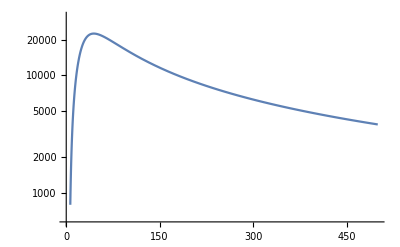

```mathematica
LogPlot[NIntegrate[arg[ER,M],{ER,1*10^-6,30*10^-6}],{M,0,500}]
```

```mathematica
(*Just replicating what EventRate does and trying to match it to what DiffCrossSection does*)
EventRate[NT_,ρchi_,qqGeV_,vve_,vv0_,vvesc_]:=Block[{FFTemp,ERTemp,bb,qq},

bb=bHO;
qq=qqGeV*GeV;
PrintLag[];

FFTemp=E^(-2y) FFfinal[DensityMatrix,JIso,TIso]/.q->qq/.y->((qq bb)/2)^2/.b->bb;

(*FFTemp=FormFactor[((qq bb)/2)^2,bb,v];*)
ERTemp=Coefficient[FFTemp,v,0] Fv0MBcutoff[vve/vv0,vmin/vv0,vvesc/vv0]/vv0+Coefficient[FFTemp,v,2]FvsqMBcutoff[vve/vv0,vmin/vv0,vvesc/vv0]*vv0;
Print["Your event rate is"];
Return[NT ρchi M/(32π mchi^3 mN) ERTemp/.vmin->qq/(2μT[mchi,M])]/.FormalReplace
]
(*M refers to isotope mass number (# of nucleons), 
mchi is the dark matter particle mass and μT is the reduced mass
of the target
μT[mchi_, M_]:= mchi M mN/(mchi+M mN)
*)

DiffCrossSection[ERkeV_,vv_]:=Block[{FFTemp,ER,bb,qq},
bb=bHO;
ER=ERkeV*10^(-6)*GeV;
qq=Sqrt[2M*(mN/GeV)*ERkeV]*10^(-3)GeV;

FFTemp=E^(-2y) FFfinal[DensityMatrix,JIso,TIso]/.q->qq/.y->((qq bb)/2)^2/.b->bb/.v->vv;

Print["Your cross-section is"];
Return[M/(32π vv^2 mchi^2 mN) FFTemp(*/.vmin->qq/(2μT[mchi,M])*)]/.FormalReplace//MyChop
];

Return[NT ρchi M/(32π mchi^3 mN) ERTemp/.vmin->qq/(2μT[mchi,M])]/.FormalReplace

EventRate/(NT ρchi M/(32π mchi^3 mN) ERTemp/.vmin->qq/(2μT[mchi,M]))


DiffCrossSection[ERkeV_,vv_]=mchi(NT ρchi v^2 )^-1* (FFTemp/ERTemp)*EventRate
EventRate=DiffCrossSection*(ERTemp/FFTemp)*(NT ρchi v^2/mchi)


ERTemp=Coefficient[FFTemp,v,0] Fv0MBcutoff[vve/vv0,vmin/vv0,vvesc/vv0]/vv0+Coefficient[FFTemp,v,2]FvsqMBcutoff[vve/vv0,vmin/vv0,vvesc/vv0]*vv0;
FFTemp
```